TOV for Neutron stars. Equation of state: 
p = α ψ^γ
ρ = ψ + α/(γ-1)ψ^γ
The units are such that
4πG = c = ρ_*=1
Where ρ_* is the energy density equivalent of one neutron per square femtometers.

```mathematica
α=0.5;
```

```mathematica
γ=2;
```

```mathematica
A=√2-1; (*This is the core psi parameter!*)
```

```mathematica
P[ψ_] = α*ψ^γ;
```

```mathematica
ρ[ψ_]=ψ + α/(γ-1)ψ^γ;
```

```mathematica
ϵ=0.0001;
```

```mathematica
L=30;
```

```mathematica
TOVeqs:=NDSolve[{α*γ*ψ[r]^(γ-1)*ψ'[r]+((ρ[ψ[r]] + P[ψ[r]])*(m[r] + 4*π*r^3*P[ψ[r]]))/(4*π*r^2-2*r*m[r])==0,m'[r]==4π*r^2*(ψ[r]+α/(γ-1)ψ[r]^γ),ψ[ϵ]==A,m[ϵ]==4*π*ρ[A]*ϵ^3/3},{ψ,m},{r,ϵ,L}];
```

```mathematica
sol=TOVeqs;
```

```mathematica
R = FindRoot[ψ[r]/.sol,{r, 2}][[1, 2]]
```

2.15116

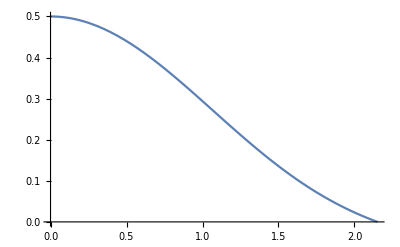

```mathematica
Plot[ρ[ψ[r]/.sol], {r, ϵ, R}]
```